Core code used to make figures which have Blot quantification.

Written By Joshua Riback.

Accompanying data can be found on figshare (to run put this file in the same  directory). 

(Note: In many cases axes are removed and added in manually in inkscape or powerpoint)

# RNase Quantification

Code to Import the data for RNase Quantification

```mathematica
dat=Import[NotebookDirectory[]<>"RNase qunatification.txt","Table"]
```

{{Fraction,Treatment,Rnase1,intensity},{T,30,-,6852},{P8,30,-,1253},{P100,30,-,2663},{S,30,-,4458},{T,42,-,5115},{P8,42,-,2992},{P100,42,-,4110},{S,42,-,3519},{T,46,-,5062},{P8,46,-,4164},{P100,46,-,3405},{S,46,-,959},{T,30,+,4386},{P8,30,+,492},{P100,30,+,228},{S,30,+,3335},{T,42,+,3203},{P8,42,+,2228},{P100,42,+,2186},{S,42,+,2903},{T,46,+,4321},{P8,46,+,3895},{P100,46,+,2923},{S,46,+,931}}

```mathematica
DAT=Association[(ToString[#[[1]]<>" "<>ToString[#[[2]]]<>#[[3]]]->#[[4]])&/@dat]
```

<|Fraction TreatmentRnase1→intensity,T 30-→6852,P8 30-→1253,P100 30-→2663,S 30-→4458,T 42-→5115,P8 42-→2992,P100 42-→4110,S 42-→3519,T 46-→5062,P8 46-→4164,P100 46-→3405,S 46-→959,T 30+→4386,P8 30+→492,P100 30+→228,S 30+→3335,T 42+→3203,P8 42+→2228,P100 42+→2186,S 42+→2903,T 46+→4321,P8 46+→3895,P100 46+→2923,S 46+→931|>

Output table showing values used to make figure in paper

```mathematica
Grid[Prepend[Flatten[Table[{x,y,DAT["S "<>x<>y]/(DAT["S "<>x<>y]+DAT["P8 "<>x<>y]+DAT["P100 "<>x<>y]),DAT["P100 "<>x<>y]/(DAT["S "<>x<>y]+DAT["P8 "<>x<>y]+DAT["P100 "<>x<>y]),DAT["P8 "<>x<>y]/(DAT["S "<>x<>y]+DAT["P8 "<>x<>y]+DAT["P100 "<>x<>y])},{x,{"30","42","46"}},{y,{"+","-"}}],1]//N,{"Temp","RNase?","  Soluble\nProportion","   P_100\nProportion","   P_8\nProportion"}]]
```

Temp | RNase? |   Soluble
Proportion |    P_100
Proportion |    P_8
Proportion
30 | + | 0.822441 | 0.0562269 | 0.121332
30 | - | 0.532362 | 0.318008 | 0.14963
42 | + | 0.396747 | 0.298756 | 0.304496
42 | - | 0.331325 | 0.386969 | 0.281706
46 | + | 0.120145 | 0.37721 | 0.502646
46 | - | 0.112453 | 0.399273 | 0.488274

Code to produce figure used in paper.

```mathematica
COLORS={GrayLevel[0],RGBColor[0.857359, 0.131106, 0.132128],RGBColor[0.471412, 0.108766, 0.527016]};
```

```mathematica
Table[ListPlot[
Table[{{0,DAT["S "<>x<>y]/(DAT["S "<>x<>y]+DAT["P8 "<>x<>y]+DAT["P100 "<>x<>y])},{1,DAT["P100 "<>x<>y]/(DAT["S "<>x<>y]+DAT["P8 "<>x<>y]+DAT["P100 "<>x<>y])},{2,DAT["P8 "<>x<>y]/(DAT["S "<>x<>y]+DAT["P8 "<>x<>y]+DAT["P100 "<>x<>y])}},{y,{"-","+"}}],PlotRange->{{-0.25,2.25},{0,1}}
,ImageSize->128
,PlotMarkers->{Automatic,8}
,PlotStyle->Table[{COLORS[[i]],AbsoluteThickness[1.6]},{i,3}]
,Joined->True,FrameTicks->{{Flatten[Table[{i+0.5j (*Round[miny,10^-SIGFIG]*),If[j==0,""(*Style[dy i+miny(*PaddedForm[N[Round[dy,10^-SIGFIG]i]+Round[miny,10^-SIGFIG],{3,SIGFIG}]*),Black]*),""],{0.0,If[j==0,0.05,0.025]}},{i,0,11},{j,0,1}],1],None}
,{Flatten[Table[{ i+0j ,If[j==0,""(*Style[d i,Black]*),""],{0.0,If[j==0,0.035,0.015]}},{i,-1,50},{j,0,1}],1],None}}
,FrameTicksStyle->Directive[{Black,AbsoluteThickness[0.8]}]
,PlotRangeClipping->True
,Axes->False
,Frame->True
,AspectRatio->1
,FrameStyle->AbsoluteThickness[0.8]
,BaseStyle->{Black,AbsoluteThickness[0.8],FontFamily->"Arial"}
(*FrameLabel->{Style[""(*"Wavelength (nm)"*),Black,25,FontFamily->"Arial"],Style[""(*"mdeg"*),Black,25,FontFamily->"Arial"]}*)],{x,{"30","42","46"}}]
```

{-Graphics-,-Graphics-,-Graphics-}

# P domain Mutant Quantification

First replicate data import

```mathematica
tmp=Association[{#[[1]]<>ToString[#[[3]]]<>#[[2]]->#[[4]]}&/@Import[NotebookDirectory[]<>"Pdom_mut_TSP_rep2_blot.txt","Table"][[2;;]]];
```

```mathematica
Table[{a,tmp[a<>"42"<>"P"]/(2tmp[a<>"42"<>"T"])},{a,{"I","L","M","WT","A","PT2","dP"}}]
```

{{I,0.420641},{L,0.334537},{M,0.320385},{WT,0.303366},{A,0.0794623},{PT2,0.0660349},{dP,0.157323}}

2nd replicate data import

```mathematica
tmp2=Association[{#[[1]]<>ToString[#[[3]]]<>#[[2]]->#[[4]]}&/@Import[NotebookDirectory[]<>"Pdom_mut_TSP_rep1_blot.txt","Table"][[2;;]]]
```

<|I'30'T→2683,I'30'S→2132,I'30'P→1902,L'30'T→3136,L'30'S→2564,L'30'P→1802,WT'30'T→3870,WT'30'S→2936,WT'30'P→1858,M'30'T→3096,M'30'S→2891,M'30'P→2116,A'30'T→3856,A'30'S→3291,A'30'P→1554,PT2'30'T→3726,PT2'30'S→2968,PT2'30'P→1378,dP'30'T→1099,dP'30'S→1246,dP'30'P→194,I'42'T→1166,I'42'S→1056,I'42'P→2240,L'42'T→1389,L'42'S→1086,L'42'P→2684,WT'42'T→1952,WT'42'S→1993,WT'42'P→2458,M'42'T→2706,M'42'S→2560,M'42'P→2946,A'42'T→3371,A'42'S→2845,A'42'P→2183,PT2'42'T→3235,PT2'42'S→2492,PT2'42'P→1582,dP'42'T→820,dP'42'S→932,dP'42'P→710,WT4'30'T→1379,WT16'30'T→471,I4'42'P→1395,I16'42'P→459|>

```mathematica
Table[{a,tmp2[a<>"'42'"<>"P"]/(4.tmp2[a<>"'42'"<>"T"])},{a,{"I","L","M","WT","A","PT2","dP"}}]
```

{{I,0.480274},{L,0.483081},{M,0.272173},{WT,0.314805},{A,0.161896},{PT2,0.122257},{dP,0.216463}}

Load Tmix from other file

```mathematica
Tdemixs2=Tdouble[#]&/@{"Pab1_MVtoI_15uM_DLSbuffpH6p4","Pab1_MVtoL_15uM_pH6p4","Pab1_VtoM_15uM_pH6p4","Pab1_15uM_DLSbuffpH6p4","Pab1_MVtoA_15uM_pH6p4_4_14_15_1","Pab1_hydroFY_to_AGPNQ_15uM_pH6p5","Pab1dP_15uM_pH6p4"};
```

Finally the figure

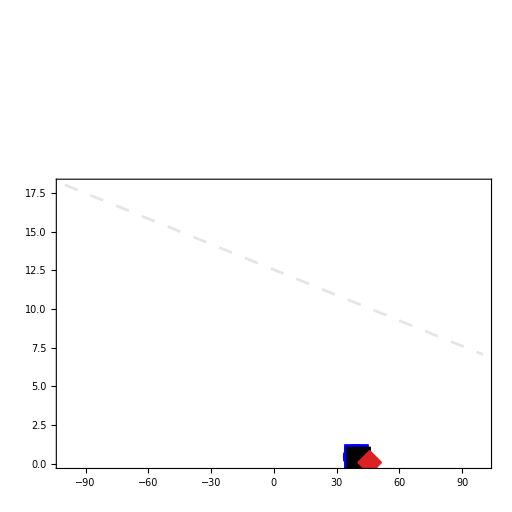

```mathematica
Module[{maxx=38.5,minx=46.5,maxy=0,miny=0.5,dat2=Flatten[{Transpose[{Tdemixs2,Pelet1}],Transpose[{Tdemixs2,Pelet2}]},1],
α2,names2={"M_8V_4→I","M_8V_4→L","G_12→P","V_4→M","WT","M_8V_4→A","M_8V_4→\n         Q_8G_2A_2","M_8V_4F_8Y_4→\n         Q_10G_4A_3P_3N_2"}},
α2=LinearModelFit[dat2,x,x];
Show[ListPlot[{#}&/@dat2
,PlotStyle->Black
,PlotMarkers->Append[COLORZ[[{7,8,6,1,4(*2*),3}]],Style["●",Purple,25]](*PlotMarkers->Table[{If[TrueQ[COLORZ[[i]]==Lighter[RGBColor[0.266122, 0.486664, 0.802529]]],"▼",If[TrueQ[COLORZ[[i]]==GrayLevel[0]],"○","★"]],If[TrueQ[delta[[i]]==None],10,25]},{i,Length[names2]}]*)
,ImageSize->512
,AspectRatio->1
,ImagePadding->{{(125),(20)},{75,10}}
,Joined->False
,Frame->True
,BaseStyle->{Black,25,FontFamily->"Arial",Thickness[0.8]}
,FrameTicks->{{Flatten[Table[{0.5i+0.25j ,"",{0.001,0.6If[j==0,0.05,0.025]}},{i,0,100},{j,0,4}],1](*Flatten[Table[{Floor[(maxy-miny)/3]i+Floor[(maxy-miny)/3]/3 j ,If[j==0,Style[Floor[(maxy-miny)/3]i,Black],""],{0.001,0.6If[j==0,0.05,0.025]}},{i,0,100},{j,0,3}],1]*),None}
,{Flatten[Table[{5i+2.5j ,"",{0.001,0.6If[j==0,0.05,0.025]}},{i,0,100},{j,0,4}],1](*Flatten[Table[{5i+j ,If[j==0,Style[5i,Black],""],{0.0,If[j==0,0.035,0.015]}},{i,0,50},{j,0,4}],1]*),None}}
,FrameTicksStyle->{{Directive[{Black,AbsoluteThickness[0.8]}],None},{Directive[{Black,AbsoluteThickness[0.8]}],None}}
,PlotRange->{{minx,maxx},{miny,maxy}}
,PlotStyle->Directive[{Black,Thickness[1.6]}]
,Axes->False
,FrameStyle->AbsoluteThickness[0.8](*Prolog->Table[Inset[Style[names2[[i]],Bold,COLORZ[[i]],FontSize->15,TextAlignment->Center,FontFamily->"Arial"],dat[[i]]+{{0.75,-1.1},{1.5,-0.8},{0.1,0.5}(*"G_12→P"*),{1.5,-0.25}(*"V_4→M"*),{1,-0.5}(*"WT"*),{-1.5,0.1}(*"M_8V_4→A"*),{1.5,-1.5}(*"Polar Tract 1"*),{-3.6,-1}(*"Polar Tract 2"*)}[[i]],{Center,Bottom}],{i,Length[names2]}]*),
Epilog->Inset[Style["r^2="<>ToString[PaddedForm[0.9514132751063241,{3,2}]],Bold,Black,FontSize->25,TextAlignment->Center,FontFamily->"Arial"],{-42.5,32},{Center,Bottom}]
,FrameLabel->{Style[""(*"T_agg of Pab1 Mutant (°C)"*),Black,25,FontFamily->"Arial"],Rotate[Style[""(*"R_g\n(Å)"*),Black,25,FontFamily->"Arial"],-Pi/2]}],Plot[α2[x]+10,{x,-100,100},PlotStyle->(Directive[Black,Opacity[0.1],AbsoluteThickness[2],AbsoluteDashing[10]])(*PlotStyle->Directive[{AbsoluteDashing[{10,10}],Thickness[0.015],Black}]*)]]]
```